### Exercise 1

This graph can be represented as 5 different graphs:

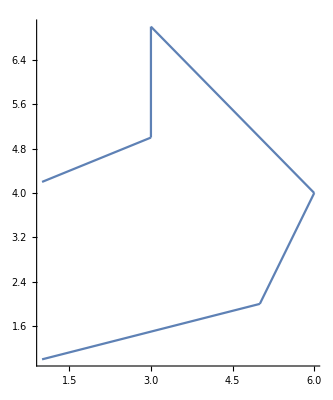

```mathematica
graph1 = Plot[(1/4)*x + 3/4, {x,1,5}, AspectRatio->Automatic];
graph2 = Plot[2x -8, {x, 5, 6}, AspectRatio->Automatic];
graph3 = Plot[-x +10, {x, 3, 6}, AspectRatio->Automatic];
graph4 = ParametricPlot[{3,y}, {y, 5,7},AspectRatio->Automatic];
graph5 = Plot[0.4x + 3.8, {x, 1, 3}, AspectRatio->Automatic];

Show[graph1, graph2, graph3, graph4, graph5, PlotRange-> All, AxesOrigin->{0,0}]
```

### Exercise 3:

In order to parametrize the intersection between the cylinder x^2+y^2= 9  and 
z = 4 -x. 

We’ll first plot our cylinder:

```mathematica
cylinder = ContourPlot3D[x^2 + y^2 - 9, {x, -4, 4}, {y, -4, 4}, {z, 0, 8}]
```

-Graphics3D-

Next we’ll plot our plane:

```mathematica
plane = Plot3D[4 - x, {x, -4,4}, {y, -4,4}]
```

-Graphics3D-

Then plotting them together:

```mathematica
Show[cylinder, plane]
```

-Graphics3D-

Now in order to parametrize this graph we need to understand the parametrization of the cylinder first. We are given the graph x^2+y^2= 9  thus we can represent that as a parametric function as such:

<3cost(t), 3sin(t)>

So, to find the intersection between this cylinder and the plane z = 4 -x, it is as such: z = 4 -x  = 4 - 3cos(t). 

Therefore, the final parametrization can be given as so:

```mathematica
f[t_] = {3Cos[t], 3Sin[t], 4-3Cos[t]};
ParametricPlot3D[f[t], {t, -4, 4}]
```

-Graphics3D-

### Exercise 7:

So we are given a helix in this picture and we must replicate this.

Now the parametric equations of a conical spiral are given as such:=

x = t r cos(a t)
	y = t r sin (a t)
	z = t

```mathematica
ParametricPlot3D[{Cos[65t],Sin[65t], t},{t,-1,1},AspectRatio->Automatic]
```

-Graphics3D-

By playing around around with the a value I’ve made a helix that is around 20 revolutions (through just plug and chug).  

Now the question is how do we get it as a double cone? We’ll play around with the r value now.

```mathematica
ParametricPlot3D[{t*Cos[65t],t*Sin[65t], t},{t,-1,1},AspectRatio->Automatic]
```

-Graphics3D-

Thus, multiplying the x and y parametric equations with t gave us the double cone shape that we wanted and now we have our double cone that has around 20 revolutions.